# Dynamics of precession

## 1. The free precession solution (J^2>2 EI_2)

```mathematica
Solve[(I3-I1)/I1==ϵ && (I3(I2-I1))/(I1(I3-I2))==δ,{I2,I3}]
```

{{I2→(I1 (1+δ) (1+ϵ))/(1+δ+ϵ),I3→I1 (1+ϵ)}}

```mathematica
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1 (1+ϵ);
Simplify[(I1*I2)/((I3-I1)(I3-I2))]
```

(1+δ)/ϵ^2

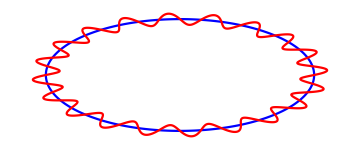

s.pdf

```mathematica
a=PolarPlot[{1,1+1/10 Sin[20t]},{t,0,2Pi},Axes->False,Background->White,ImageSize->{360,150},AspectRatio->Full,PlotStyle->{Blue,Red}]
SetDirectory[NotebookDirectory[]];
Export["s.pdf",a]
```

```mathematica
m={b1,b2,b3}
```

{b1,b2,b3}

```mathematica
M=EulerMatrix[{ϕ,θ,ψ},{3,1,3}]
```

{{Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ],-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ],Sin[θ] Sin[ϕ]},{Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]},{Sin[θ] Sin[ψ],Cos[ψ] Sin[θ],Cos[θ]}}

```mathematica
mi=Simplify[M.m]
```

{Cos[ϕ] (b1 Cos[ψ]-b2 Sin[ψ])+Sin[ϕ] (b3 Sin[θ]-Cos[θ] (b2 Cos[ψ]+b1 Sin[ψ])),-b3 Cos[ϕ] Sin[θ]+Cos[θ] Cos[ϕ] (b2 Cos[ψ]+b1 Sin[ψ])+Sin[ϕ] (b1 Cos[ψ]-b2 Sin[ψ]),b3 Cos[θ]+Sin[θ] (b2 Cos[ψ]+b1 Sin[ψ])}

```mathematica
Coefficient[mi[[3]],{b1}]*b1+Coefficient[mi[[3]],{b2}]*b2+Coefficient[mi[[3]],{b3}]*b3
```

{b3 Cos[θ]+b2 Cos[ψ] Sin[θ]+b1 Sin[θ] Sin[ψ]}

```mathematica
TeXForm[b3 Cos[θ]+b2 Cos[ψ] Sin[θ]+b1 Sin[θ] Sin[ψ]]
```

\text{b1} \sin (\theta ) \sin (\psi )+\text{b2} \sin (\theta ) \cos (\psi )+\text{b3} \cos (\theta
   )